```mathematica
PercentForm@(439/222351)
```

439/222351

```mathematica
439/222351
```

439/222351

```mathematica
Sin[√(x^2-1)]
```

```mathematica
PercentForm[Out[2]]
```

439/222351

```mathematica
PercentForm@N@Out@2
```

0.1974%

```mathematica
StreamPlot[{
3 x^2,
Sin[1/(√(x^2-1))]
},{x,y}∈Rectangle[{-1,-1},{1,1}],
StreamColorFunction->Hue]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
StreamPlot[{
3 x^2,
Sin[√(x^2-1)]
},{x,y}∈Rectangle[{-1,-1},{1,1}],
StreamColorFunction->Hue]
```

StreamPlot[{3 x^2,Sin[√(x^2-1)]},{x,y}∈Rectangle[{-1,-1},{1,1}],StreamColorFunction→Hue]

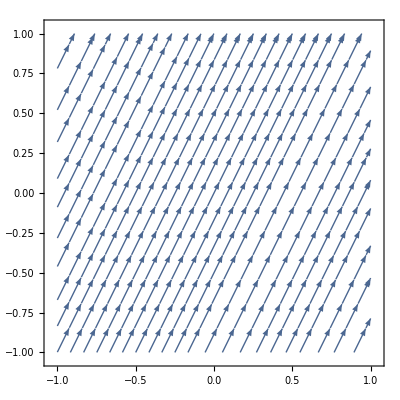

```mathematica
StreamPlot[{1,2}, {x,-1, 1}, {y, -1, 1}]
```

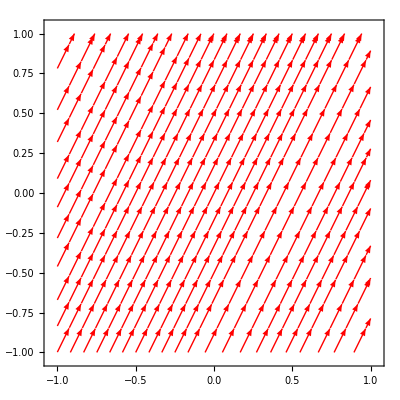

```mathematica
StreamPlot[
{1,2}, 
{x,-1, 1},
 {y, -1, 1},
StreamColorFunction->Hue]
```

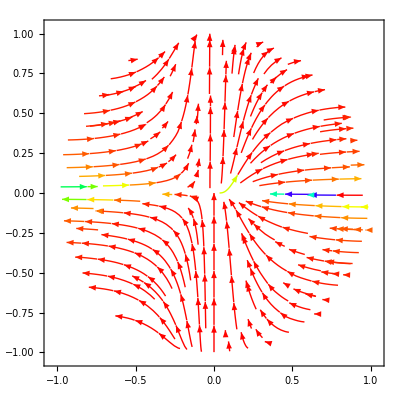

```mathematica
StreamPlot[{
3 x^2/y
,
√(1-x^2-y^2)
}, 
{x,-1, 1},
 {y, -1, 1},
StreamColorFunction->Hue]
```

Power::infy: Infinite expression 1/0. encountered.

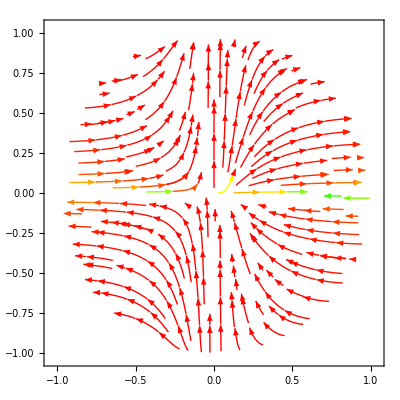

```mathematica
StreamPlot[{
3 x^2/y
,
√(1-x^2-y^2)
}, 
Element[{x,y} ,Disk[]],
StreamColorFunction->Hue]
```

```mathematica
StreamPlot[{
3 x^2/y
,
√(1-x^2-y^2)
}, 
Element[{x,y} ,Rectangle[{-1,-1},{1,1}]],
StreamColorFunction->Hue]
```

$Aborted

```mathematica
StreamPlot[{
(3 x^2)/y
,
√(1-x^2-y^2)
}, 
Element[{x,y} ,Rectangle[{-1,-1},{1,1}]],
StreamColorFunction->Hue]
```

$Aborted

Power::infy: Infinite expression 1/0. encountered.

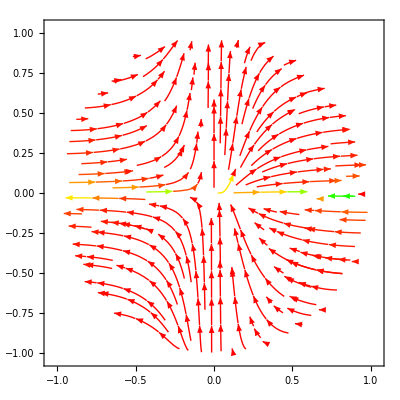

```mathematica
StreamPlot[{
(3 x^2)/y
,
√(1-x^2-y^2)
}, 
Element[{x,y} ,Disk[]],
StreamColorFunction->Hue]
```

```mathematica
StreamPlot[{
(3 x^2)/y
,
√(1-x^2-y^2)
}, 
{x,-1,1},{y-1,1},
StreamColorFunction->Hue]
```

StreamPlot::pllim: Range specification {y-1,1} is not of the form {x, xmin, xmax}.

General::stop: Further output of StreamPlot::pllim will be suppressed during this calculation.

StreamPlot[{(3 x^2)/y,√(1-x^2-y^2)},{x,-1,1},{y-1,1},StreamColorFunction→Hue]

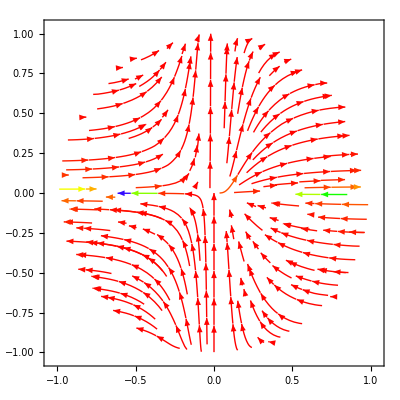

```mathematica
StreamPlot[{
(3 x^2)/y
,
√(1-x^2-y^2)
}, {x,-1,1},{y,-1,1},
StreamColorFunction->Hue]
```

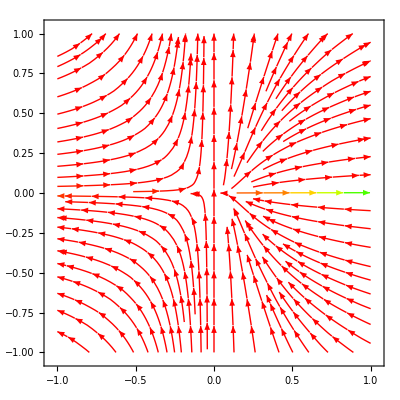

```mathematica
StreamPlot[{
(3 x^2)/y
,
√(1+x^2+y^2)
}, {x,-1,1},{y,-1,1},
StreamColorFunction->Hue]
```

```mathematica
Manipulate[
Show[{
StreamPlot[{
(3 x^2)/y
,
√(1+x^2+y^2)
}, {x,-1,1},{y,-1,1},
StreamColorFunction->Hue],
ListPlot[{{-1/2,-1/2},{a,b}}]}],
{a, -1, 1}, {b, -1, 1}]
```

```mathematica
<<VariationalMethods`
```

```mathematica
VariationalD[y[x] √(1+y'[x]^2),y[x],x]
```

(1+y'[x]^2-y[x] y''[x])/((1+y'[x]^2)^(3/2))

```mathematica
VariationalMethods`VariationalD[y[x] √(1+y'[x]^2),y[x],x]
```

(1+y'[x]^2-y[x] y''[x])/((1+y'[x]^2)^(3/2))

```mathematica
VariationalMethods`VariationalD[√(1+y'[x]^2),y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))

```mathematica
VariationalMethods`VariationalD[√(1+y'[x]^2),y[x],x]==0
```

-y''[x]/((1+y'[x]^2)^(3/2))==0

```mathematica
DSolve[-y''[x]/((1+y'[x]^2)^(3/2))==0,{y[x],y[x]},{x}]
```

{{y[x]→C[1]+x C[2]}}

```mathematica
Trace@DSolve[-y''[x]/((1+y'[x]^2)^(3/2))==0,{y[x],y[x]},{x}]
```

{{{{{{{{1/2,1/2},3/2,3/2},(1+y'[x]^2)^(3/2)},1/((1+y'[x]^2)^(3/2)),1/((1+y'[x]^2)^(3/2))},y''[x]/((1+y'[x]^2)^(3/2)),y''[x]/((1+y'[x]^2)^(3/2))},-y''[x]/((1+y'[x]^2)^(3/2)),-y''[x]/((1+y'[x]^2)^(3/2))},-y''[x]/((1+y'[x]^2)^(3/2))==0},DSolve[-y''[x]/((1+y'[x]^2)^(3/2))==0,{y[x],y[x]},{x}],{{y[x]→C[1]+x C[2]}}}

```mathematica
VariationalMethods`VariationalD[√(1+y'[x]^2),y[x],x]==0
```

```mathematica
DSolve[VariationalMethods`VariationalD[√(1+y'[x]^2),y[x],x]==0,{y[x]},{x}]
```

{{y[x]→C[1]+x C[2]}}

```mathematica
FullSimplify[
Normalize[{1,3 x^2}].
Normalize[{1,f'[x]}],
{x,f[x],f'[x]}∈Reals]
```

(1+3 x^2 f'[x])/(√((1+9 x^4) (1+f'[x]^2)))

```mathematica
FullSimplify[
Normalize[{1,3 x^2}].
Normalize[{1,f'[x]}],
{x,f[x],f'[x]}∈Reals]==0
```

(1+3 x^2 f'[x])/(√((1+9 x^4) (1+f'[x]^2)))==0

```mathematica
DSolve[(1+3 x^2 f'[x])/(√((1+9 x^4) (1+f'[x]^2)))==0,{f[x]},{x}]
```

{{f[x]→1/(3 x)+C[1]}}

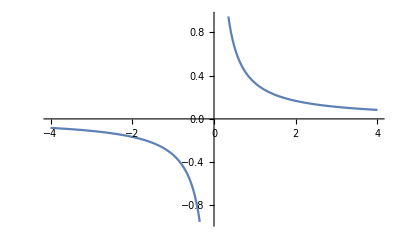

```mathematica
Plot[1/(3 x),{x,-4,4}]
```

```mathematica
FullSimplify[
Normalize[{1,3 x^2}].
Normalize[{1,f'[x]}],
{x,f[x],f'[x]}∈Reals]==1
```

(1+3 x^2 f'[x])/(√((1+9 x^4) (1+f'[x]^2)))==1

```mathematica
DSolve[(1+3 x^2 f'[x])/(√((1+9 x^4) (1+f'[x]^2)))==1,{f[x]},{x}]
```

{{f[x]→x^3+C[1]}}

```mathematica
VariationalD[(1+3 x^2 f'[x])/(√((1+9 x^4) (1+f'[x]^2))),f[x],x]
```

((1+9 x^4) (-6 x-18 x^3 f'[x]^3+(1+9 x^4) f''[x]+9 x^2 f'[x] (-2 x+(1+9 x^4) f''[x])-2 f'[x]^2 (3 x+(1+9 x^4) f''[x])))/(((1+9 x^4) (1+f'[x]^2))^(5/2))

```mathematica
Cancel[%32]
```

1/(((1+9 x^4) (1+f'[x]^2))^(5/2))(1+9 x^4) (-6 x-18 x^3 f'[x]-6 x f'[x]^2-18 x^3 f'[x]^3+f''[x]+9 x^4 f''[x]+9 x^2 f'[x] f''[x]+81 x^6 f'[x] f''[x]-2 f'[x]^2 f''[x]-18 x^4 f'[x]^2 f''[x])

```mathematica
((1+9 x^4) (-6 x-18 x^3 f'[x]^3+(1+9 x^4) f''[x]+9 x^2 f'[x] (-2 x+(1+9 x^4) f''[x])-2 f'[x]^2 (3 x+(1+9 x^4) f''[x])))/(((1+9 x^4) (1+f'[x]^2))^(5/2))==0
```

((1+9 x^4) (-6 x-18 x^3 f'[x]^3+(1+9 x^4) f''[x]+9 x^2 f'[x] (-2 x+(1+9 x^4) f''[x])-2 f'[x]^2 (3 x+(1+9 x^4) f''[x])))/(((1+9 x^4) (1+f'[x]^2))^(5/2))==0

```mathematica
DSolve[%34,{f[x],f[x]},{x}]
```

DSolve[((1+9 x^4) (-6 x-18 x^3 f'[x]^3+(1+9 x^4) f''[x]+9 x^2 f'[x] (-2 x+(1+9 x^4) f''[x])-2 f'[x]^2 (3 x+(1+9 x^4) f''[x])))/(((1+9 x^4) (1+f'[x]^2))^(5/2))==0,{f[x],f[x]},{x}]

```mathematica
VariationalD[f'[x],f[x],x]
```

0

```mathematica
VariationalD[g[f[x]],f[x],x]
```

g'[f[x]]

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Dt[Laplacian[f[x],{x}]]
```

Dt[x] f^(3)[x]

```mathematica
EulerEquations[√(1+y'[x]^2),y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))==0

```mathematica
DSolve[-y''[x]/((1+y'[x]^2)^(3/2))==0,{y[x],y[x]},{x}]
```

{{y[x]→C[1]+x C[2]}}

```mathematica
EulerEquations[1/2 m r^2 θ'[t]^2+m g r Cos[θ[t]],θ[t],t]
```

-m r (g Sin[θ[t]]+r θ''[t])==0

```mathematica
DSolve[-m r (g Sin[θ[t]]+r θ''[t])==0,{θ[t]},{r}]
```

DSolve::dvnoarg: The function θ[t] appears with no arguments.

DSolve[-m r (g Sin[θ[t]]+r θ''[t])==0,{θ[t]},{r}]

```mathematica
DSolve[-m r (g Sin[θ[t]]+r θ''[t])==0,{θ[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[t]→2 JacobiAmplitude[(√(2 g+r C[1]) (t+C[2]))/(2 √r),(4 g)/(2 g+r C[1])]},{θ[t]→-2 JacobiAmplitude[(t √(2 g+r C[1]))/(2 √r)+(√(2 g+r C[1]) C[2])/(2 √r),(4 g)/(2 g+r C[1])]}}

```mathematica
LinguisticAssistant
```

Failure[…]

```mathematica
EulerEquations[f[y''[x],y'[x],y[x],x],y[x],x]
```

f^(0,0,1,0)[y''[x],y'[x],y[x],x]-f^(0,1,0,1)[y''[x],y'[x],y[x],x]-y'[x] f^(0,1,1,0)[y''[x],y'[x],y[x],x]-y''[x] f^(0,2,0,0)[y''[x],y'[x],y[x],x]+f^(1,0,0,2)[y''[x],y'[x],y[x],x]+y''[x] f^(1,0,1,0)[y''[x],y'[x],y[x],x]+2 y'[x] f^(1,0,1,1)[y''[x],y'[x],y[x],x]+y'[x]^2 f^(1,0,2,0)[y''[x],y'[x],y[x],x]+2 y''[x] f^(1,1,0,1)[y''[x],y'[x],y[x],x]+2 y'[x] y''[x] f^(1,1,1,0)[y''[x],y'[x],y[x],x]+y''[x]^2 f^(1,2,0,0)[y''[x],y'[x],y[x],x]+y^(4)[x] f^(2,0,0,0)[y''[x],y'[x],y[x],x]+2 y^(3)[x] f^(2,0,0,1)[y''[x],y'[x],y[x],x]+2 y'[x] y^(3)[x] f^(2,0,1,0)[y''[x],y'[x],y[x],x]+2 y''[x] y^(3)[x] f^(2,1,0,0)[y''[x],y'[x],y[x],x]+(y^(3)[x])^2 f^(3,0,0,0)[y''[x],y'[x],y[x],x]==0

```mathematica
DSolve[%46,{y[x],y[x],y[x],y[x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x]},{x}]
```

DSolve::litarg: To avoid possible ambiguity, the arguments of the dependent variable in f[y''[x],y'[x],y[x],x] should literally match the independent variables.

DSolve[f^(0,0,1,0)[y''[x],y'[x],y[x],x]-f^(0,1,0,1)[y''[x],y'[x],y[x],x]-y'[x] f^(0,1,1,0)[y''[x],y'[x],y[x],x]-y''[x] f^(0,2,0,0)[y''[x],y'[x],y[x],x]+f^(1,0,0,2)[y''[x],y'[x],y[x],x]+y''[x] f^(1,0,1,0)[y''[x],y'[x],y[x],x]+2 y'[x] f^(1,0,1,1)[y''[x],y'[x],y[x],x]+y'[x]^2 f^(1,0,2,0)[y''[x],y'[x],y[x],x]+2 y''[x] f^(1,1,0,1)[y''[x],y'[x],y[x],x]+2 y'[x] y''[x] f^(1,1,1,0)[y''[x],y'[x],y[x],x]+y''[x]^2 f^(1,2,0,0)[y''[x],y'[x],y[x],x]+y^(4)[x] f^(2,0,0,0)[y''[x],y'[x],y[x],x]+2 y^(3)[x] f^(2,0,0,1)[y''[x],y'[x],y[x],x]+2 y'[x] y^(3)[x] f^(2,0,1,0)[y''[x],y'[x],y[x],x]+2 y''[x] y^(3)[x] f^(2,1,0,0)[y''[x],y'[x],y[x],x]+(y^(3)[x])^2 f^(3,0,0,0)[y''[x],y'[x],y[x],x]==0,{y[x],y[x],y[x],y[x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x],f[y''[x],y'[x],y[x],x]},{x}]

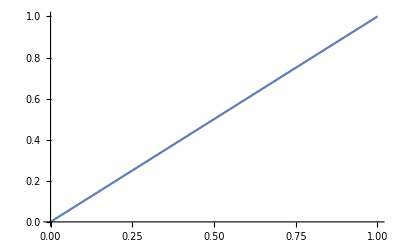

```mathematica
Plot[x, {x,0, 1}]
```

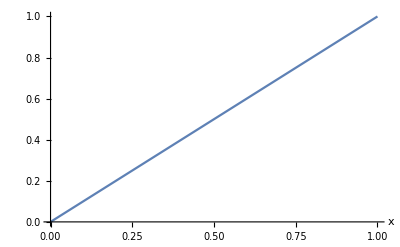

```mathematica
Plot[x, {x,0, 1},AxesLabel->Automatic]
```

```mathematica
Plot[x, {x,0, 1},AxesLabel->Automatic, PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Plot[x, {x,0, 1},AxesLabel->Automatic, PlotLegends->"Expressions"]
```

```mathematica
Plot[x,x∈Line[{{0,10}}]]
```

Plot::idomdim: x∈Line[{{0,10}}] does not have a valid dimension as a plotting domain.

Plot[x,x∈Line[{{0,10}}]]

```mathematica
Plot[x,x∈Line[{0,10}]]
```

Plot::idomdim: x∈Line[{0,10}] does not have a valid dimension as a plotting domain.

Plot[x,x∈Line[{0,10}]]

```mathematica
Plot[x,x∈Line[{{0,0},{1,1}}]]
```

Plot::idomdim: x∈Line[{{0,0},{1,1}}] does not have a valid dimension as a plotting domain.

Plot[x,x∈Line[{{0,0},{1,1}}]]

```mathematica
Plot[x, {x,0, 1},AxesLabel->Automatic]
```

-Graphics-

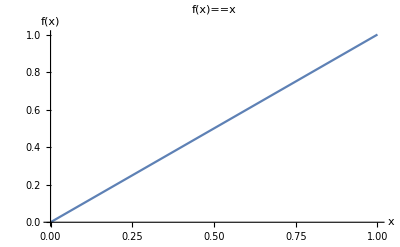

```mathematica
Show[%54,AxesLabel->{HoldForm[x],HoldForm[f[x]]},PlotLabel->HoldForm[f[x]==x],LabelStyle->{FontFamily->"DejaVu Sans",GrayLevel[0]}]
```

```mathematica
Plot[x, {x,0, 1},
AxesLabel->{HoldForm[x],HoldForm[f[x]]},PlotLabel->HoldForm[f[x]==x],LabelStyle->{FontFamily->"DejaVu Sans",GrayLevel[0]}]
```

-Graphics-

```mathematica
Plot[x, {x,0, 1},
AxesLabel->{HoldForm[x],HoldForm[f[x]]},PlotLabel->HoldForm[f[x]==x],LabelStyle->{FontFamily->"DejaVu Sans",GrayLevel[0]}]
```

-Graphics-

```mathematica
a^2+b^2==c^2
```

a^2+b^2==c^2

```mathematica
a^2+b^2==c^2/.{a->1,b->1}
```

2==c^2

```mathematica
Reduce[2==c^2]
```

c==-√2||c==√2

```mathematica
FindInstance[2==c^2,{c}]
```

{{c→-√2}}

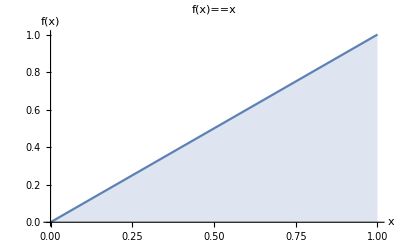

```mathematica
Plot[x, {x,0, 1},
AxesLabel->{HoldForm[x],HoldForm[f[x]]},PlotLabel->HoldForm[f[x]==x],LabelStyle->{FontFamily->"DejaVu Sans",GrayLevel[0]}, Filling->Axis]
```

```mathematica
√2==∫_0^1 f[x]ⅆx
```

√2==∫_0^1 f[x]ⅆx

```mathematica
FindInstance[√2==∫_0^1 f[x]ⅆx,{x}]
```

FindInstance[√2==∫_0^1 f[x]ⅆx,{x}]

```mathematica
Reduce[√2==∫_0^1 f[x]ⅆx]
```

∫_0^1 f[x]ⅆx==√2

```mathematica
√2==∫_0^1 √(1+f'[x])ⅆx
```

√2==∫_0^1 √(1+f'[x])ⅆx

```mathematica
Reduce[√2==∫_0^1 √(1+f'[x])ⅆx]
```

∫_0^1 √(1+f'[x])ⅆx==√2

```mathematica
D[√2,x]==D[∫_0^1 √(1+f'[x])ⅆx,x]
```

True

```mathematica
D[∫_0^1 √(1+f'[x])ⅆx,x]
```

0

```mathematica
D[√2,x]==D[∫_0^1 y[x]ⅆx,x]
```

True

```mathematica
∫_0^1 √(1+1)ⅆx
```

√2

```mathematica
CompanyData[]
```

{01 Communique Laboratory,01Cyberaton,1-800-Attorney,1.Maj Drvodjelska,1 oktobar,1000Mercis,1000memories,100e.com,Lion Rock Group,1010data,10-20 Media,104,10BestThings,10CMS,10gen,111,1168 Contruction,11 bit studios,11 mart,11i Solutions,1300 Smiles,Limbach Holdings,1347 PIH,1366 Technologies,1369 Construction,138 Student Living,140Fire,140 Proof,1414 Degrees,141 Capital,169 ST.,1-800-Flowers.com,1847 Holdings,1867 Western Financial,1895 Bancorp of Wisconsin,1957 & Co,1C,1DayMakeover,Garfin Holding,1 maj,1PM Industries,1 Production Film,1Spatial,1calendar,1nkemia IUCT Group,1pm,1st Group,1st Capital Bank,1st Century Bancshrs,1st Colonial Bancorp,1st Constitution,1st Holdings,1st NRG,1st Prestige Wealth Mgmt,1st RED AG,1st Source,1st Summit Bancorp,1st United Bancorp,1time Holdings,20/20 Global,myTaste,2050 Motors,2080 Media,20:20 Mobile Group,20 Microns,20x200,21Cake Food,21GRAMS,21 Lady Co,Twentyfirst Century Mngt,21Vianet Group,21st Century Technology,22. decembar,2242749 Ontario,22 Capital,22nd Century Group,235 Holdings,23andMe,23press,24/7 Gaming Group,24/7 Kid Doc,24Holdings,24 Hour Fitness Worldwide,24 Ianuarie,24 Media Network,24SevenOffice Scandinavia,24x7 Learning,2C PARTNERS,2CRSI,77181,Zosano Pharma,Zota Health Care,Zotefoams,Zounds,Zoy Home Furnishing Co,zozi,Zrak - optoelektronika,Zrak,Zrebcin Motesice,Zscaler,Ztest Electronics,Zts Inmart,Zts Sabinov,Zuari Agro Chemicals,Zuari Global,Zuberance,Zublin Immobilien Holding,Vincenzo Zucchi,Zue,Officiis Properties,Zug Estates Holding,Zuger,Zuiko,Zuk Elzab,ZUKEN,zulily,zulily,Zulu Tek,Zumbox,Zume Life,Zumeo.com,Zumiez,Zumobi,Zumtobel Group,Zungwon En-Sys,Zunicom,Zuoan Fashion,Zuoli Kechuang,Zuora,Zuora,Zupa turistickoo,Zupljanka,Zur Rose Group,Zur Shamir Holdings,Zurich Insurance Group,Zurvita Holdings,Zutec Holding,Zuu Co,Zuujit,Zuvvu,Zvecevo Prehrambena,Zvelo,Zvezda-Helios,Zvezda Fabrika ogledala,Zvezdara,Zvezdara Avala,Zvi Sarfati & Sons Inv,Zvijezda,Zvizd,Zvornik - stan,Zvornikputevi,Zwack Unicum,Zwahlen et Mayr,Zweemie,Zwei Co,zweitgeist,Zwipe,Zyden Gentec,Zydus Wellness,Zygo,Zyken - NightCove,Zylog Systems,Hawkstone Mining,Zyme Solutions,Zymetis,Zymeworks,Zymeworks,ZymoGenetics,Zyncro Tech,Zynerba Pharmaceuticals,Zynex,Zynga,Zyngenia,Zyrox Mining Intl,Zyrra,Global Unicorn Hldgs,Zytronic,vLex}
 |  |  |  |

```mathematica
CompanyData["Apple"]
```

Missing[UnknownEntity,{Company,Apple}]

```mathematica
CompanyData["SampleEntities"]
```

{Apple,Pfizer,Novartis,Bank of America,Goldman Sachs Group,Berkshire Hathaway,eBay,Delta Air Lines,AT&T,Monsanto}

```mathematica
Entity["Company", "Apple"]
```

Entity[Company,Apple]

```mathematica
CompanyData[Entity["Company", "Apple"],"Properties"]
```

{accounts payable,accounts receivable,accumulated depreciation,additional paid in capital,address,amortization,assets turnover,beginning cash position,capital expenditures,cash,cash and cash equivalents,cash dividends paid,cash equivalents,cash flow from continuing financing activities,cash flow from continuing investing activities,cash flow from continuing operating activities,cash flow from discontinued operation,cash from discontinued financing activities,cash from discontinued investing activities,change in accrued expense,change in interest payable,change in inventory,change in payable,change in tax payable,change in working capital,change in cash and cash equivalents,change in receivables,city,common shares,common stock,common stock issuance,common stock payments,coordinates,corporate structure,cost of revenue,current accrued expenses,current assets,current debt,current liabilities,current notes payable,current ratio,deferred assets,deferred costs,deferred tax assets,defunct date,depreciation,depreciation amortization depletion,depreciation and amortization,earnings before interest and tax,earnings before interest tax depreciation and amortization,total employees,end cash position,entity classes,equity investments,financial health grade,financial leverage,financing cash flow,former names,founding date,free cash flow,general and administrative expense,goodwill,goodwill and other intangible assets,gross loan,gross margin,gross properties plants and equipment,gross profit,growth grade,held to maturity securities,company logo,income tax payable,sector,interest bearing deposits assets,interest bearing deposits liabilities,interest expense,interest expense from non-operating activities,interest expense from operating activities,interest income,interest income from non-operating activities,interest income from operating activities,interest payable,inventory,inventory turnover,investing cash flow,long-term debt,long-term debt issuance,long-term debt payments,debt to capital ratio,long-term investments,metropolitan area,minority interest,money market investments,name,net business purchase and sale,net income,net income earned by common stockholders,net income from continuous operations,net income from discontinuous operations,net income from extraordinary,net income growth,net intangibles purchase and sale,net interest income,net investment income,net investment purchase and sale,net loan,net margin,net non-operating interest income and expense,net operating interest income and expense,fixed assets,net purchase and sale of properties plants and equipments,net technology purchase and sale,non-current accrued expenses,non-current notes receivables,non-interest expense,non-interest income,notes receivable,operating cash flow,operating expense,operating income,operating income growth,operating margin,operating revenue,other financial instruments,other income expense,other intangible assets,other short-term investments,ownership type,position,postal code,predecessor companies,preferred stock,preferred stock dividends,preferred stock issuance,preferred stock payments,pre-tax income,profitability grade,purchase of business,purchase of equity securities,purchase of fixed maturity securities,purchase of intangibles,purchase of investment,purchase of long-term investments,purchase of properties plants and equipments,purchase of short-term investments,purchase of technology,research and development,retained earnings,revenue growth,revenue per employee,return on assets,return on equity,sales of business,sale of intangibles,sales of investment,sale of long-term investments,sales of properties plants and equipments,sales of short-term investments,sales of equity securities,sales of fixed maturity securities,selling and marking expense,selling general and administration,short-term debt issuance,short-term debt payments,status,stockholders equity,successor companies,tax provision,total assets,total debt,total deposits,total expenses,total investments,total liabilities,total non-current assets,total non-current liabilities,total revenue,total tax payable,trading liabilities,trading securities,treasury stock,unearned income,website,working capital}

```mathematica
CompanyData[Entity["Company", "Apple"],"City"]
```

Missing[UnknownEntity,{Company,Apple}]

```mathematica
CompanyData[Entity["Company","Apple::5zkjq"], "Employees"]
```

132000 people

```mathematica
EntityClass["Country", "Population" ->GreaterEqual[10000000]]
```

EntityClass[Country,Population→True]

```mathematica
EntityClass["Country", "Population" ->GreaterThan[10000000]]
```

EntityClass[Country,Population→GreaterThan[10000000]]

```mathematica
EntityClass["Country", "Population" ->GreaterThan[10000000]]["Population", "EntityAssociated"]
```

{Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}],Missing[UnknownProperty,{Country,Population,{},EntityAssociated}]}

{Apple,Pfizer,Novartis,Bank of America,Goldman Sachs Group,Berkshire Hathaway,eBay,Delta Air Lines,AT&T,Monsanto}

TotalRevenue

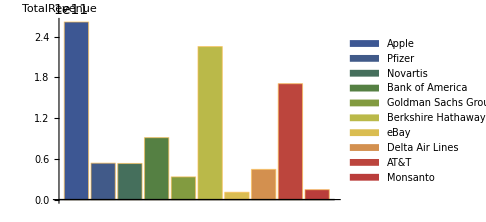

```mathematica
sample=CompanyData["SampleEntities"]
prop="TotalRevenue"
BarChart[CompanyData[sample,prop,"EntityAssociation"],ChartStyle->"DarkRainbow",ImageSize->Medium,AxesLabel->prop,ChartLegends->CommonName[sample]]
```

```mathematica
ℓ(f)=∫ba1+f′(x)2−−−−−−−−√dx
```

Integrate::nodiffd: ∫ba1 cannot be interpreted. Integrals are entered in the form ∫fⅆx, ∫_a^b , or ∫_(vars ∈ region) , where ⅆ is entered as EscddEsc.

```mathematica
EntityClass["Country", "Population" ->GreaterThan[10000000]]["Population", "EntityAssociation"]
```

<|China→1409517397 people,India→1339180127 people,United States→324459463 people,Indonesia→263991379 people,Brazil→209288278 people,Pakistan→197015955 people,Nigeria→190886311 people,Bangladesh→164669751 people,Russia→143989754 people,Mexico→129163276 people,Japan→127484450 people,Ethiopia→104957438 people,Philippines→104918090 people,Egypt→97553151 people,Vietnam→95540800 people,Germany→82114224 people,Democratic Republic of the Congo→81339988 people,Iran→81162788 people,Turkey→80745020 people,Thailand→69037513 people,United Kingdom→66181585 people,France→64979548 people,Italy→59359900 people,Tanzania→57310019 people,South Africa→56717156 people,Myanmar→53370609 people,South Korea→50982212 people,Kenya→49699862 people,Colombia→49065615 people,Spain→46354321 people,Argentina→44271041 people,Ukraine→44222947 people,Uganda→42862958 people,Algeria→41318142 people,Sudan→40533330 people,Iraq→38274618 people,Poland→38170712 people,Canada→36624199 people,Morocco→35739580 people,Afghanistan→35530081 people,Saudi Arabia→32938213 people,Peru→32165485 people,Venezuela→31977065 people,Uzbekistan→31910641 people,Malaysia→31624264 people,Angola→29784193 people,Mozambique→29668834 people,Nepal→29304998 people,Ghana→28833629 people,Yemen→28250420 people,Madagascar→25570895 people,North Korea→25490965 people,Australia→24450561 people,Ivory Coast→24294750 people,Cameroon→24053727 people,Taiwan→23626456 people,Niger→21477348 people,Sri Lanka→20876917 people,Romania→19679306 people,Burkina Faso→19193382 people,Malawi→18622104 people,Mali→18541980 people,Syria→18269868 people,Kazakhstan→18204499 people,Chile→18054726 people,Zambia→17094130 people,Netherlands→17035938 people,Guatemala→16913503 people,Ecuador→16624858 people,Zimbabwe→16529903 people,Cambodia→16005373 people,Senegal→15850567 people,Chad→14899994 people,Somalia→14742523 people,Guinea→12717176 people,South Sudan→12575714 people,Rwanda→12208407 people,Tunisia→11532127 people,Cuba→11484636 people,Belgium→11429336 people,Benin→11175692 people,Greece→11159773 people,Bolivia→11051600 people,Haiti→10981229 people,Burundi→10864245 people,Dominican Republic→10766998 people,Czech Republic→10618303 people,Portugal→10329506 people|>

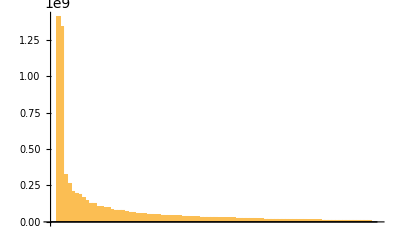

```mathematica
BarChart[
EntityClass["Country",
 "Population" ->GreaterThan[10000000]]["Population", "EntityAssociation"]]
```

```mathematica
ChartStyle->"DarkRainbow"
```

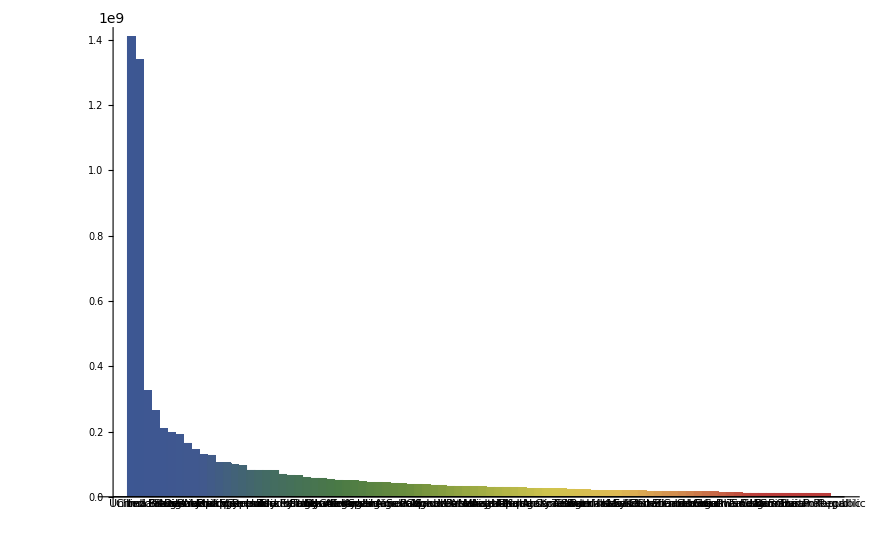

```mathematica
BarChart[
EntityClass["Country",
 "Population" ->GreaterThan[10000000]]["Population", "EntityAssociation"],
ChartStyle->"DarkRainbow", ChartLabels->Automatic]
```

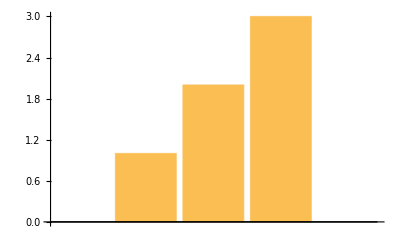

```mathematica
BarChart[{1,2,3}]
```

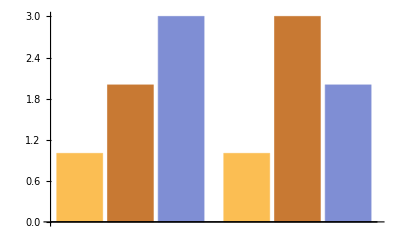

```mathematica
BarChart[{{1,2,3},{1,3,2}}]
```

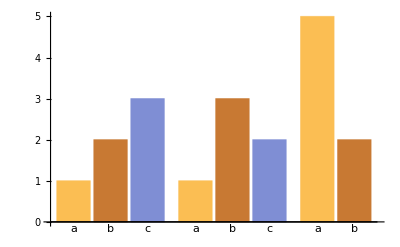

```mathematica
BarChart[{{1,2,3},{1,3,2},{5,2}},ChartLabels->{"a","b","c"}]
```

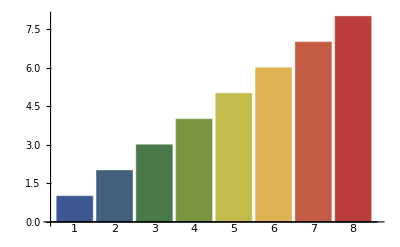

```mathematica
BarChart[Range[8],ChartStyle->"DarkRainbow", ChartLabels->Range[8]]
```

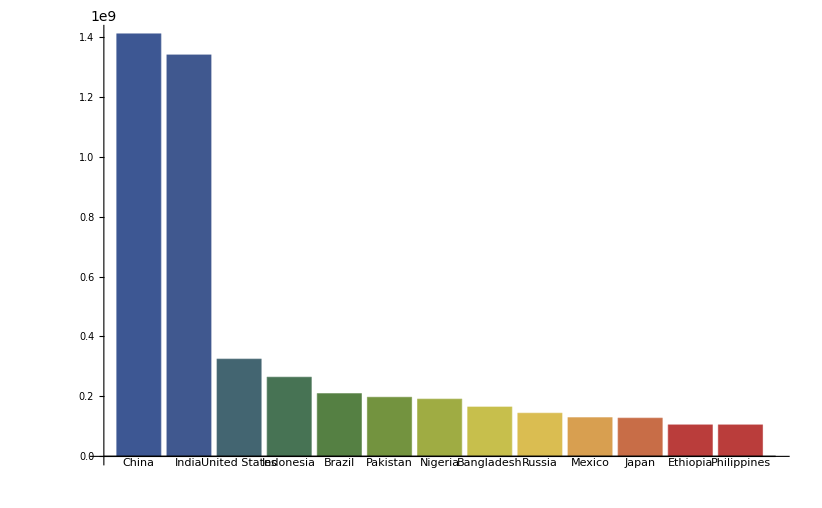

```mathematica
BarChart[
EntityClass["Country",
 "Population" ->GreaterThan[100000000]]["Population", "EntityAssociation"],
ChartStyle->"DarkRainbow", ChartLabels->Automatic]
```

```mathematica
EntityValue[Entity["GeographicRegion","Europe"][EntityProperty["GeographicRegion","Countries"]],EntityProperty["Country","Population"]]
```

{2930187 people,76965 people,8735453 people,9468338 people,11429336 people,3507017 people,7084571 people,4189353 people,10618303 people,5733551 people,1309632 people,49290 people,5523231 people,64979548 people,82114224 people,34571 people,11159773 people,65605 people,9721559 people,335025 people,4761657 people,84287 people,59359900 people,95732 people,1859203 people,1949670 people,37922 people,2890297 people,583455 people,2083159 people,430835 people,4051212 people,38695 people,628960 people,17035938 people,5305383 people,38170712 people,10329506 people,19679306 people,143989754 people,33400 people,8790574 people,5447662 people,2079976 people,46354321 people,2637 people,9910701 people,8476005 people,44222947 people,66181585 people,792 people}

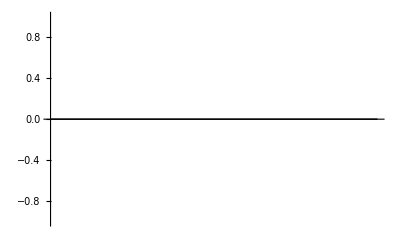

```mathematica
BarChart[
EntityClass["Country",
 "Population" ->And[LessThan[100000000],GreaterThan[50000000]]]["Population", "EntityAssociation"],
ChartStyle->"DarkRainbow", ChartLabels->Automatic]
```

```mathematica
EntityValue[Entity["GeographicRegion","Europe"][EntityProperty["GeographicRegion","Countries"]],{"EntityAssociation",EntityProperty["Country","Population"]}]
```

{{Missing[UnknownProperty,{Country,EntityAssociation}],2930187 people},{Missing[UnknownProperty,{Country,EntityAssociation}],76965 people},{Missing[UnknownProperty,{Country,EntityAssociation}],8735453 people},{Missing[UnknownProperty,{Country,EntityAssociation}],9468338 people},{Missing[UnknownProperty,{Country,EntityAssociation}],11429336 people},{Missing[UnknownProperty,{Country,EntityAssociation}],3507017 people},{Missing[UnknownProperty,{Country,EntityAssociation}],7084571 people},{Missing[UnknownProperty,{Country,EntityAssociation}],4189353 people},{Missing[UnknownProperty,{Country,EntityAssociation}],10618303 people},{Missing[UnknownProperty,{Country,EntityAssociation}],5733551 people},{Missing[UnknownProperty,{Country,EntityAssociation}],1309632 people},{Missing[UnknownProperty,{Country,EntityAssociation}],49290 people},{Missing[UnknownProperty,{Country,EntityAssociation}],5523231 people},{Missing[UnknownProperty,{Country,EntityAssociation}],64979548 people},{Missing[UnknownProperty,{Country,EntityAssociation}],82114224 people},{Missing[UnknownProperty,{Country,EntityAssociation}],34571 people},{Missing[UnknownProperty,{Country,EntityAssociation}],11159773 people},{Missing[UnknownProperty,{Country,EntityAssociation}],65605 people},{Missing[UnknownProperty,{Country,EntityAssociation}],9721559 people},{Missing[UnknownProperty,{Country,EntityAssociation}],335025 people},{Missing[UnknownProperty,{Country,EntityAssociation}],4761657 people},{Missing[UnknownProperty,{Country,EntityAssociation}],84287 people},{Missing[UnknownProperty,{Country,EntityAssociation}],59359900 people},{Missing[UnknownProperty,{Country,EntityAssociation}],95732 people},{Missing[UnknownProperty,{Country,EntityAssociation}],1859203 people},{Missing[UnknownProperty,{Country,EntityAssociation}],1949670 people},{Missing[UnknownProperty,{Country,EntityAssociation}],37922 people},{Missing[UnknownProperty,{Country,EntityAssociation}],2890297 people},{Missing[UnknownProperty,{Country,EntityAssociation}],583455 people},{Missing[UnknownProperty,{Country,EntityAssociation}],2083159 people},{Missing[UnknownProperty,{Country,EntityAssociation}],430835 people},{Missing[UnknownProperty,{Country,EntityAssociation}],4051212 people},{Missing[UnknownProperty,{Country,EntityAssociation}],38695 people},{Missing[UnknownProperty,{Country,EntityAssociation}],628960 people},{Missing[UnknownProperty,{Country,EntityAssociation}],17035938 people},{Missing[UnknownProperty,{Country,EntityAssociation}],5305383 people},{Missing[UnknownProperty,{Country,EntityAssociation}],38170712 people},{Missing[UnknownProperty,{Country,EntityAssociation}],10329506 people},{Missing[UnknownProperty,{Country,EntityAssociation}],19679306 people},{Missing[UnknownProperty,{Country,EntityAssociation}],143989754 people},{Missing[UnknownProperty,{Country,EntityAssociation}],33400 people},{Missing[UnknownProperty,{Country,EntityAssociation}],8790574 people},{Missing[UnknownProperty,{Country,EntityAssociation}],5447662 people},{Missing[UnknownProperty,{Country,EntityAssociation}],2079976 people},{Missing[UnknownProperty,{Country,EntityAssociation}],46354321 people},{Missing[UnknownProperty,{Country,EntityAssociation}],2637 people},{Missing[UnknownProperty,{Country,EntityAssociation}],9910701 people},{Missing[UnknownProperty,{Country,EntityAssociation}],8476005 people},{Missing[UnknownProperty,{Country,EntityAssociation}],44222947 people},{Missing[UnknownProperty,{Country,EntityAssociation}],66181585 people},{Missing[UnknownProperty,{Country,EntityAssociation}],792 people}}

```mathematica
LinguisticAssistant
```

Failure[…]

```mathematica
EntityClass["Country", "Europe"]
```

Europe

```mathematica
EntityList[EntityClass["Country","Europe"]]
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

```mathematica
BarChart[
EntityClass["Language",{EntityProperty["Language","TotalSpeakers"]->TakeLargest[5]}]["EntityAssociation", EntityProperty["Language","TotalSpeakers"]],
ColorFunction->"Rainbow", ChartLabels->Automatic]
```

-Graphics-

```mathematica
EntityClass["Language",{EntityProperty["Language","TotalSpeakers"]->TakeLargest[5]}]["EntityAssociation",EntityProperty["Language","TotalSpeakers"]]
```

{Missing[Propagated,Missing[UnknownProperty,{Language,EntityAssociation}]],Missing[Propagated,Missing[UnknownProperty,{Language,EntityAssociation}]],Missing[Propagated,Missing[UnknownProperty,{Language,EntityAssociation}]],Missing[Propagated,Missing[UnknownProperty,{Language,EntityAssociation}]],Missing[Propagated,Missing[UnknownProperty,{Language,EntityAssociation}]]}

```mathematica
EntityList@EntityClass["Language",{EntityProperty["Language","TotalSpeakers"]->TakeLargest[5]}]
```

{Mandarin Chinese,English,Hindi,Spanish,Russian}

```mathematica
EntityList@
EntityClass["Country", "Europe"]
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

```mathematica
EntityList@
EntityClass["Country", "UnitedNations"]
```

{Afghanistan,Albania,Algeria,Andorra,Angola,Antigua and Barbuda,Argentina,Armenia,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bhutan,Bolivia,Bosnia and Herzegovina,Botswana,Brazil,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Central African Republic,Chad,Chile,China,Colombia,Comoros,Costa Rica,Croatia,Cuba,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Fiji,Finland,France,Gabon,Gambia,Georgia,Germany,Ghana,Greece,Grenada,Guatemala,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Israel,Italy,Ivory Coast,Jamaica,Japan,Jordan,Kazakhstan,Kenya,Kiribati,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Marshall Islands,Mauritania,Mauritius,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Zealand,Nicaragua,Niger,Nigeria,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Poland,Portugal,Qatar,Republic of the Congo,Romania,Russia,Rwanda,Saint Kitts and Nevis,Saint Lucia,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Eswatini,Sweden,Switzerland,Syria,Tajikistan,Tanzania,Thailand,Togo,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,Uruguay,Uzbekistan,Vanuatu,Venezuela,Vietnam,Yemen,Zambia,Zimbabwe}

```mathematica
EntityList@
EntityClass["Book", "English"]
```

Missing[UnknownEntityClass,{Book,English}]

```mathematica
MovieData["PulpFiction::vc263", "Properties"]
```

{rating advisory,cast,cast and roles,company,director,US box office total receipts,US daily box office change in receipts,US daily box office receipts,US daily box office rank,total daily US box office receipts,US daily number of screens,US daily average receipts per screen,US weekend box office change in receipts,US weekend box office receipts,US weekend box office rank,US weekend number of screens,US weekend average receipts per screen,US weekly box office receipts,total weekly US box office receipts,genre,highest daily average receipts per screen,best daily box office change in receipts,highest daily box office receipts,highest daily rank,maximum daily number of screens,highest weekend average receipts per screen,best weekend box office change in receipts,highest weekend box office receipts,highest weekend box office rank,maximum weekend number of screens,highest weekly US box office receipts,image,language,title,producer,production budget,release date,runtime,working title,writer}

```mathematica
Map[
#->MovieData["PulpFiction::vc263", #]&,
MovieData["PulpFiction::vc263", "Properties"]]
```

{rating advisory→for strong graphic violence and drug use, pervasive strong language and some sexuality,cast→{Bruce Willis,Samuel L. Jackson,Steve Buscemi,Amanda Plummer,Christopher Walken,Harvey Keitel,John Travolta,Maria de Medeiros,Ving Rhames,Tim Roth,Frank Whaley,Duane Whitaker,Uma Thurman,Eric Stoltz,Emil Sitka,Julia Sweeney,Paul Calderon,Quentin Tarantino,Lawrence Bender,Michael Gilden,Alexis Arquette,Rosanna Arquette,Dick Miller,Phil LaMarr,Kathy Griffin,Peter Greene,Karen Maruyama},cast and roles→{Bruce Willis→{Butch Coolidge},Samuel L. Jackson→{Jules Winnfield},Steve Buscemi→{Buddy Holly},Amanda Plummer→{Honey Bunny},Christopher Walken→{Captain Koons},Harvey Keitel→{Winston Wolf},John Travolta→{Vincent Vega},Maria de Medeiros→{Fabienne},Ving Rhames→{Marsellus Wallace},Tim Roth→{Pumpkin},Frank Whaley→{Brett},Duane Whitaker→{Maynard},Uma Thurman→{Mia Wallace},Eric Stoltz→{Lance},Emil Sitka→{Hold Hands You Lovebirds Sayer},Julia Sweeney→{Raquel},Paul Calderon→{Paul},Quentin Tarantino→{Jimmy},Lawrence Bender→{Man In Coffee Shop},Michael Gilden→{Phillip Morris Page},Alexis Arquette→{Fourth Man},Rosanna Arquette→{Jody},Dick Miller→{Monster Joe},Phil LaMarr→{Marvin},Kathy Griffin→{Hit-And-Run Witness},Peter Greene→{Zed},Karen Maruyama→{Gawker #1}},company→{Miramax,A Band Apart,Jersey Films},director→{Quentin Tarantino},US box office total receipts→1.07928762e8 $,US daily box office change in receipts→Missing[NotInCurrentRelease],US daily box office receipts→Missing[NotInCurrentRelease],US daily box office rank→Missing[NotInCurrentRelease],total daily US box office receipts→1.07928762e8 $,US daily number of screens→Missing[NotInCurrentRelease],US daily average receipts per screen→Missing[NotInCurrentRelease],US weekend box office change in receipts→Missing[NotInCurrentRelease],US weekend box office receipts→Missing[NotInCurrentRelease],US weekend box office rank→Missing[NotInCurrentRelease],US weekend number of screens→Missing[NotInCurrentRelease],US weekend average receipts per screen→Missing[NotInCurrentRelease],US weekly box office receipts→Missing[NotInCurrentRelease],total weekly US box office receipts→1.07928762e8 $,genre→{crime,drama},highest daily average receipts per screen→Missing[NotAvailable],best daily box office change in receipts→Missing[NotAvailable],highest daily box office receipts→Missing[NotAvailable],highest daily rank→Missing[NotAvailable],maximum daily number of screens→Missing[NotAvailable],highest weekend average receipts per screen→6 960.00 $,best weekend box office change in receipts→201. %,highest weekend box office receipts→9.311882e6 $,highest weekend box office rank→1,maximum weekend number of screens→1494,highest weekly US box office receipts→1.3280967e7 $,image→-Graphics-,language→{English,Spanish,French},title→Pulp Fiction,producer→{Lawrence Bender,Michael Shamberg,Stacey Sher,Danny DeVito},production budget→8.e6 $,release date→Day: Fri 14 Oct 1994,runtime→154 min,working title→Missing[NotAvailable],writer→{Quentin Tarantino,Roger Avary}}

```mathematica
Column@
Map[
#->MovieData["PulpFiction::vc263", #]&,
MovieData["PulpFiction::vc263", "Properties"]]
```

rating advisory→for strong graphic violence and drug use, pervasive strong language and some sexuality
cast→{Bruce Willis,Samuel L. Jackson,Steve Buscemi,Amanda Plummer,Christopher Walken,Harvey Keitel,John Travolta,Maria de Medeiros,Ving Rhames,Tim Roth,Frank Whaley,Duane Whitaker,Uma Thurman,Eric Stoltz,Emil Sitka,Julia Sweeney,Paul Calderon,Quentin Tarantino,Lawrence Bender,Michael Gilden,Alexis Arquette,Rosanna Arquette,Dick Miller,Phil LaMarr,Kathy Griffin,Peter Greene,Karen Maruyama}
cast and roles→{Bruce Willis→{Butch Coolidge},Samuel L. Jackson→{Jules Winnfield},Steve Buscemi→{Buddy Holly},Amanda Plummer→{Honey Bunny},Christopher Walken→{Captain Koons},Harvey Keitel→{Winston Wolf},John Travolta→{Vincent Vega},Maria de Medeiros→{Fabienne},Ving Rhames→{Marsellus Wallace},Tim Roth→{Pumpkin},Frank Whaley→{Brett},Duane Whitaker→{Maynard},Uma Thurman→{Mia Wallace},Eric Stoltz→{Lance},Emil Sitka→{Hold Hands You Lovebirds Sayer},Julia Sweeney→{Raquel},Paul Calderon→{Paul},Quentin Tarantino→{Jimmy},Lawrence Bender→{Man In Coffee Shop},Michael Gilden→{Phillip Morris Page},Alexis Arquette→{Fourth Man},Rosanna Arquette→{Jody},Dick Miller→{Monster Joe},Phil LaMarr→{Marvin},Kathy Griffin→{Hit-And-Run Witness},Peter Greene→{Zed},Karen Maruyama→{Gawker #1}}
company→{Miramax,A Band Apart,Jersey Films}
director→{Quentin Tarantino}
US box office total receipts→1.07928762e8 $
US daily box office change in receipts→Missing[NotInCurrentRelease]
US daily box office receipts→Missing[NotInCurrentRelease]
US daily box office rank→Missing[NotInCurrentRelease]
total daily US box office receipts→1.07928762e8 $
US daily number of screens→Missing[NotInCurrentRelease]
US daily average receipts per screen→Missing[NotInCurrentRelease]
US weekend box office change in receipts→Missing[NotInCurrentRelease]
US weekend box office receipts→Missing[NotInCurrentRelease]
US weekend box office rank→Missing[NotInCurrentRelease]
US weekend number of screens→Missing[NotInCurrentRelease]
US weekend average receipts per screen→Missing[NotInCurrentRelease]
US weekly box office receipts→Missing[NotInCurrentRelease]
total weekly US box office receipts→1.07928762e8 $
genre→{crime,drama}
highest daily average receipts per screen→Missing[NotAvailable]
best daily box office change in receipts→Missing[NotAvailable]
highest daily box office receipts→Missing[NotAvailable]
highest daily rank→Missing[NotAvailable]
maximum daily number of screens→Missing[NotAvailable]
highest weekend average receipts per screen→6 960.00 $
best weekend box office change in receipts→201. %
highest weekend box office receipts→9.311882e6 $
highest weekend box office rank→1
maximum weekend number of screens→1494
highest weekly US box office receipts→1.3280967e7 $
image→-Graphics-
language→{English,Spanish,French}
title→Pulp Fiction
producer→{Lawrence Bender,Michael Shamberg,Stacey Sher,Danny DeVito}
production budget→8.e6 $
release date→Day: Fri 14 Oct 1994
runtime→154 min
working title→Missing[NotAvailable]
writer→{Quentin Tarantino,Roger Avary}

```mathematica
MovieData["10RulesForSleepingAround::k89bp", "Advisory"]
```

for crude and sexual content throughout, language, nudity and some drug use

```mathematica
MovieData["10RulesForSleepingAround::k89bp", "Genres"]
```

{comedy,romance}

```mathematica
MovieData["10RulesForSleepingAround::k89bp", "Image"]
```

Missing[NotAvailable]

```mathematica
MovieData["10RulesForSleepingAround::k89bp", "Company"]
```

{Thinkfactory Media}

```mathematica
EntityValue[EntityClass["Country",{EntityProperty["Country","BoundaryLength"]->TakeLargest[10]}],EntityProperty["Country","BoundaryLength"],"EntityAssociation"]
```

<|Canada→131093. mi,Russia→36006. mi,Indonesia→35757.4 mi,Greenland→27394.4 mi,China→22771.6 mi,Philippines→22548.9 mi,United States→19857.8 mi,Japan→18486.4 mi,Norway→17205.8 mi,Australia→16006.5 mi|>

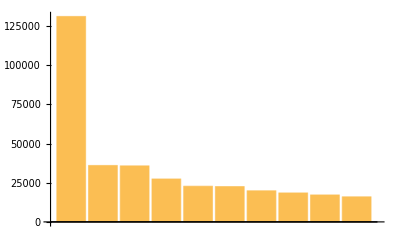

```mathematica
BarChart@
EntityValue[EntityClass["Country",{EntityProperty["Country","BoundaryLength"]->TakeLargest[10]}],EntityProperty["Country","BoundaryLength"],"EntityAssociation"]
```

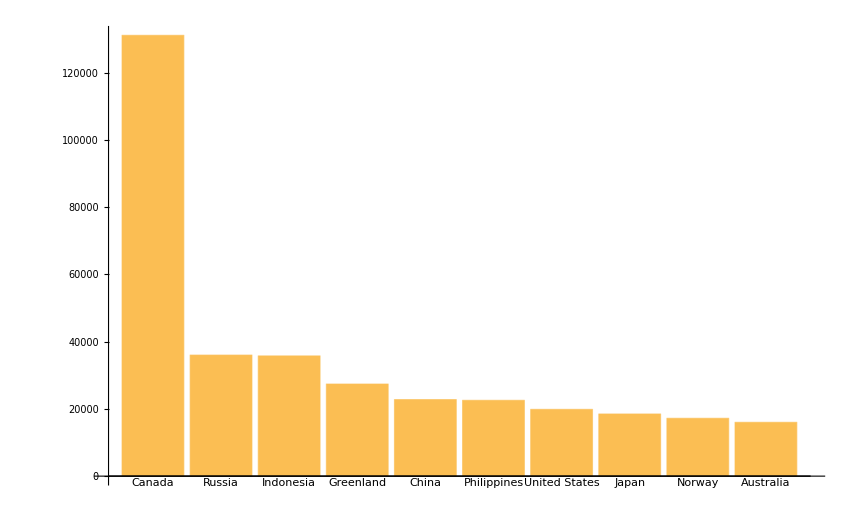

```mathematica
BarChart[
EntityValue[EntityClass["Country",{EntityProperty["Country","BoundaryLength"]->TakeLargest[10]}],EntityProperty["Country","BoundaryLength"],"EntityAssociation"],
ChartLabels->Automatic]
```

```mathematica
BarChart[
EntityValue[EntityClass["Country",{EntityProperty["Country","BoundaryLength"]->TakeLargest[10]}],EntityProperty["Country","BoundaryLength"],"EntityAssociation"],
ChartLabels->Automatic]

LinguisticAssistant
```

```mathematica
CountryData["UnitedStates", "CoastlineLength"]
```

$Aborted

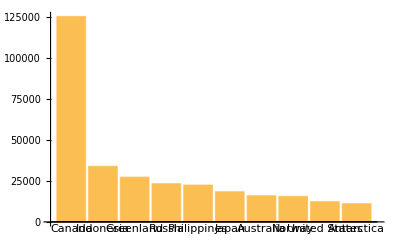

```mathematica
BarChart[
EntityValue[
EntityClass["Country",{"CoastlineLength"->TakeLargest[10]}],
"CoastlineLength","EntityAssociation"],
ChartLabels->Automatic]
```

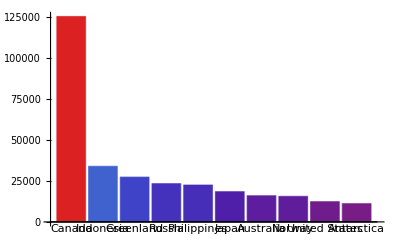

```mathematica
BarChart[
EntityValue[
EntityClass["Country",{"CoastlineLength"->TakeLargest[10]}],
"CoastlineLength","EntityAssociation"],
ChartLabels->Automatic, ColorFunction->"Rainbow"]
```

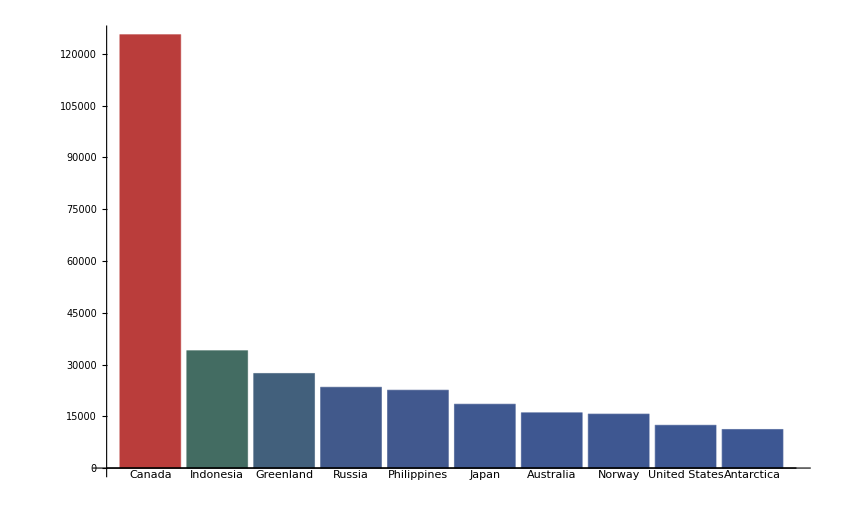

```mathematica
BarChart[
EntityValue[
EntityClass["Country",{"CoastlineLength"->TakeLargest[10]}],
"CoastlineLength","EntityAssociation"],
ChartLabels->Automatic, ColorFunction->"DarkRainbow"]
```

```mathematica
FullSimplify[
Normalize[{g'[x],h'[x]}].
Normalize[{1,f'[x]}],
{x,g'[x],h'[x],f'[x]}∈Reals]
```

(g'[x]+f'[x] h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))

```mathematica
FullSimplify[
Normalize[{g'[x],h'[x]}].
Normalize[{1,f'[x]}],
{x,g'[x],h'[x],f'[x]}∈Reals]==0
```

(g'[x]+f'[x] h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))==0

```mathematica
DSolve[(g'[x]+f'[x] h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))==0,{f[x],g[x],h[x]},{x}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[(g'[x]+f'[x] h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))==0,{f[x],g[x],h[x]},{x}]

```mathematica
DSolve[(g'[x]+f'[x] h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))==0,{f[x]},{x}]
```

{{f[x]→C[1]+-g'[K[1]]/h'[K[1]]K[1]1x}}

```mathematica
{{f[x]->C[1]+-g'[K[1]]/h'[K[1]]K[1]1x}}⟦1,1,2⟧
```

C[1]+-g'[K[1]]/h'[K[1]]K[1]1x

```mathematica
C[1]+-g'[K[1]]/h'[K[1]]K[1]1x/.K[1]->x
```

C[1]+-g'[x]/h'[x]x1x

```mathematica
C[1]+-g'[x]/h'[x]x1x
```

C[1]+-g'[x]/h'[x]x1x

```mathematica
Activate[C[1]+-g'[x]/h'[x]x1x]
```

C[1]+∫_1^x -g'[x]/h'[x]ⅆx

```mathematica
C[1]+Activate[-g'[x]/h'[x]x1x]
```

C[1]+∫_1^x -g'[x]/h'[x]ⅆx

```mathematica
DSolve[(g'[x]+f'[x] h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))==0,f[x],x]
```

{{f[x]→C[1]+-g'[K[1]]/h'[K[1]]K[1]1x}}

```mathematica
f[x_]:=C[1]+-g'[K[1]]/h'[K[1]]K[1]1x
```

```mathematica
Clear[f]
```

```mathematica
With[{C[1]=0},
C[1]+∫_1^x -g'[x]/h'[x]ⅆx]
```

With::lvset: Local variable specification {1=0} contains 1=0, which is an assignment to 1; only assignments to symbols are allowed.

With[{C[1]=0},C[1]+∫_1^x -g'[x]/h'[x]ⅆx]

```mathematica
With[{g=Exp,h=Identity},
∫_1^x -g'[x]/h'[x]ⅆx]
```

ⅇ-ⅇ^x

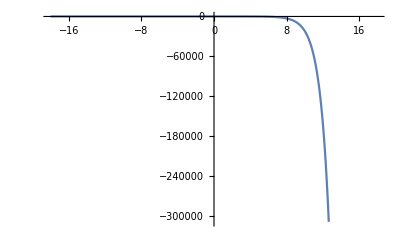

```mathematica
Plot[ⅇ-ⅇ^x,{x,-18.,18.}]
```

```mathematica
With[{g=Sin,h=Identity},
∫_1^x -g'[x]/h'[x]ⅆx]
```

Sin[1]-Sin[x]

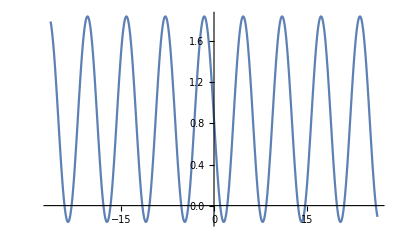

```mathematica
Plot[Sin[1]-Sin[x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Activate[-g'[K[1]]/h'[K[1]]K[1]1x]
```

∫_1^x -g'[K[1]]/h'[K[1]]ⅆK[1]

```mathematica
∫_1^a -g'[x]/h'[x]ⅆx
```

∫_1^a -g'[x]/h'[x]ⅆx

```mathematica
∂_a ∫_1^a -g'[x]/h'[x]ⅆx
```

-g'[a]/h'[a]

```mathematica
With[{g=Sin,h=Cos},
∫_1^a -g'[x]/h'[x]ⅆx]
```

Integrate::idiv: Integral of Cot[1+x] does not converge on {0,π}.

Integrate::idiv: Integral of Cot[x] does not converge on {1,a}.

∫_1^a Cot[x]ⅆx

```mathematica
With[{g=Sin,h=Identity},
∫_1^a -g'[x]/h'[x]ⅆx]
```

Sin[1]-Sin[a]

```mathematica
With[{g=Sin,h=Sinc},
∫_1^a -g'[x]/h'[x]ⅆx]
```

$Aborted

```mathematica
With[{g=Sin,h=√Exp[#]&},
∫_1^a -g'[x]/h'[x]ⅆx]
```

ConditionalExpression[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))),ⅇ^a≥0]

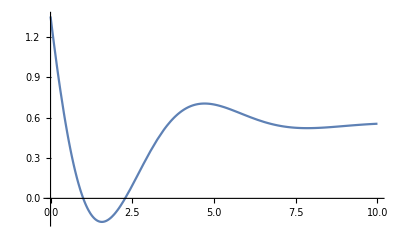

```mathematica
Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 10}]
```

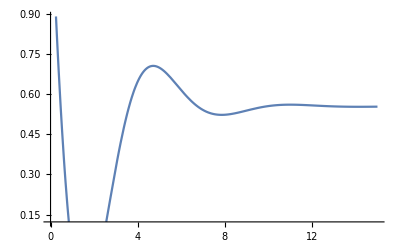

```mathematica
Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}]
```

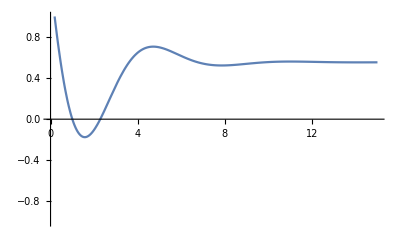

```mathematica
Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1,1}]
```

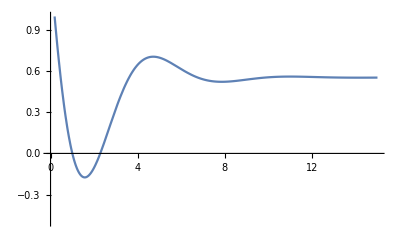

```mathematica
Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1/2,1}]
```

```mathematica
Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-4/10,1}]
```

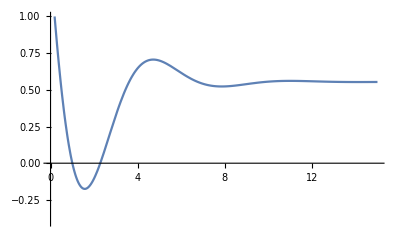
```mathematica
-Graphics-Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1/2,1}]
```

```mathematica
Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1/2,1}]
```

```mathematica
Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1/2,1}]Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1/2,1}]Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1/2,1}]Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1/2,1}]Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1/2,1}]Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1/2,1}]{a,Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1/2,1}] 0, 15}, PlotRange->{-1/2,1}]
```

```mathematica
Plot[-2 ((2 (Cos[1]-2 Sin[1]))/(5 √ⅇ)-(2 (Cos[a]-2 Sin[a]))/(5 √(ⅇ^a))), {a, 0, 15}, PlotRange->{-1/2,1}]
```

-Graphics-